# QED calculation: Peskin Sec. 5

## e^+e^-→μ^+μ^- (QED): Peskin P.131-136

-Graphics-

### Initialization

You should choose English.

```mathematica
Exit[];
```

```mathematica
$Language="English";
SetDirectory[FileNameJoin[{$HomeDirectory,"Documents","Dropbox","FeynLecture"}]]
```

/Users/misho/Documents/Dropbox/FeynLecture

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.7

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 4 Jan 12

FormCalc 7.3

by Thomas Hahn

last revised 12 Jan 12

### Create Topology

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

> Top. 4: 1 diagram

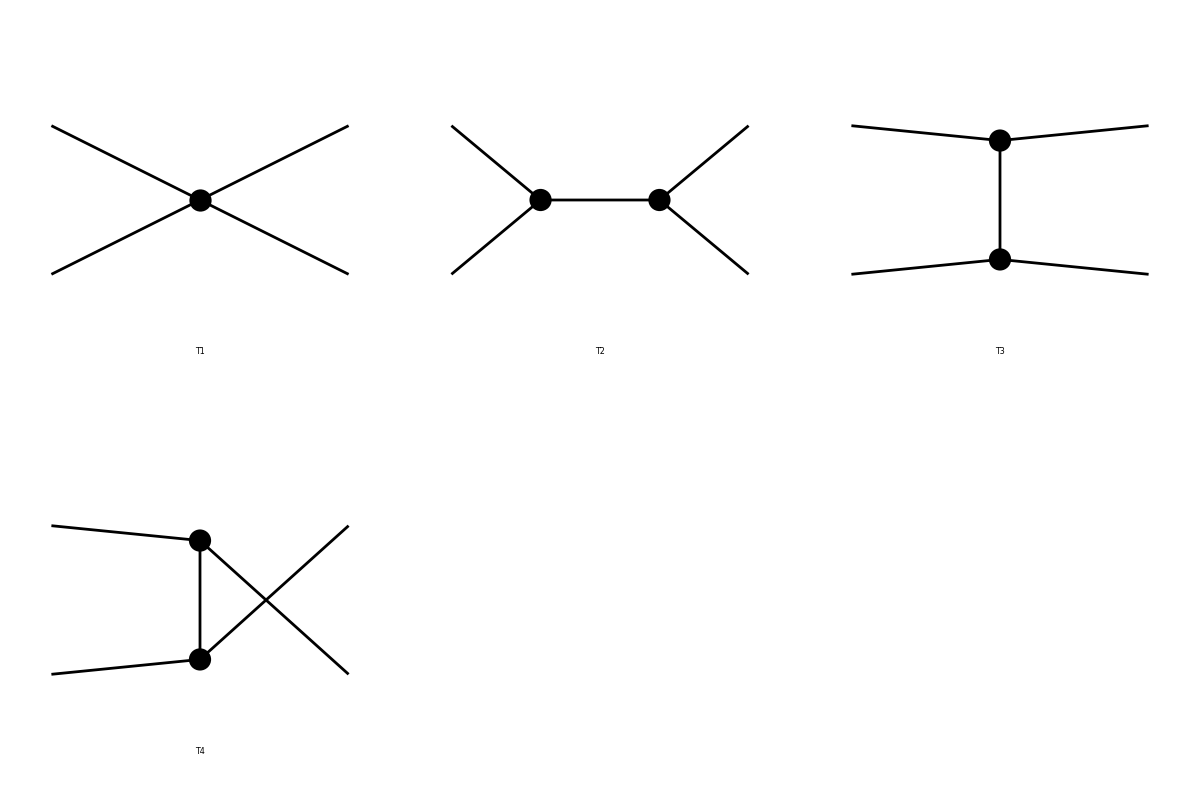

FeynArtsGraphics[2→2][([T1] | [T2] | [T3]
[T4] | Null | Null
Null | Null | Null)]

```mathematica
topologies=CreateTopologies[0,2->2]
Paint[topologies]
```

### Insert Particles

Manual P.74 has a list of the particles in the (default) SM model.

```mathematica
diagrams=InsertFields[topologies,{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]},InsertionLevel->{Classes}]
```

loading generic model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.7/Models/Lorentz.gen

> $SVMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.7/Models/SM.mod

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 114 counter terms of order 1

> 6 counter terms of order 2

classes model {SM} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 4 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

in total: 4 Classes insertions

TopologyList[Process→{F[2,{1}],-F[2,{1}]}→{F[2,{2}],-F[2,{2}]},Model→{SM},GenericModel→{Lorentz},InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→S]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→S[1]],FeynmanGraph[1,Classes==2][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→S[2]]],FeynmanGraph[1,Generic==2][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→V[1]],FeynmanGraph[1,Classes==2][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→V[2]]]]]

> Top. 1: 4 diagrams

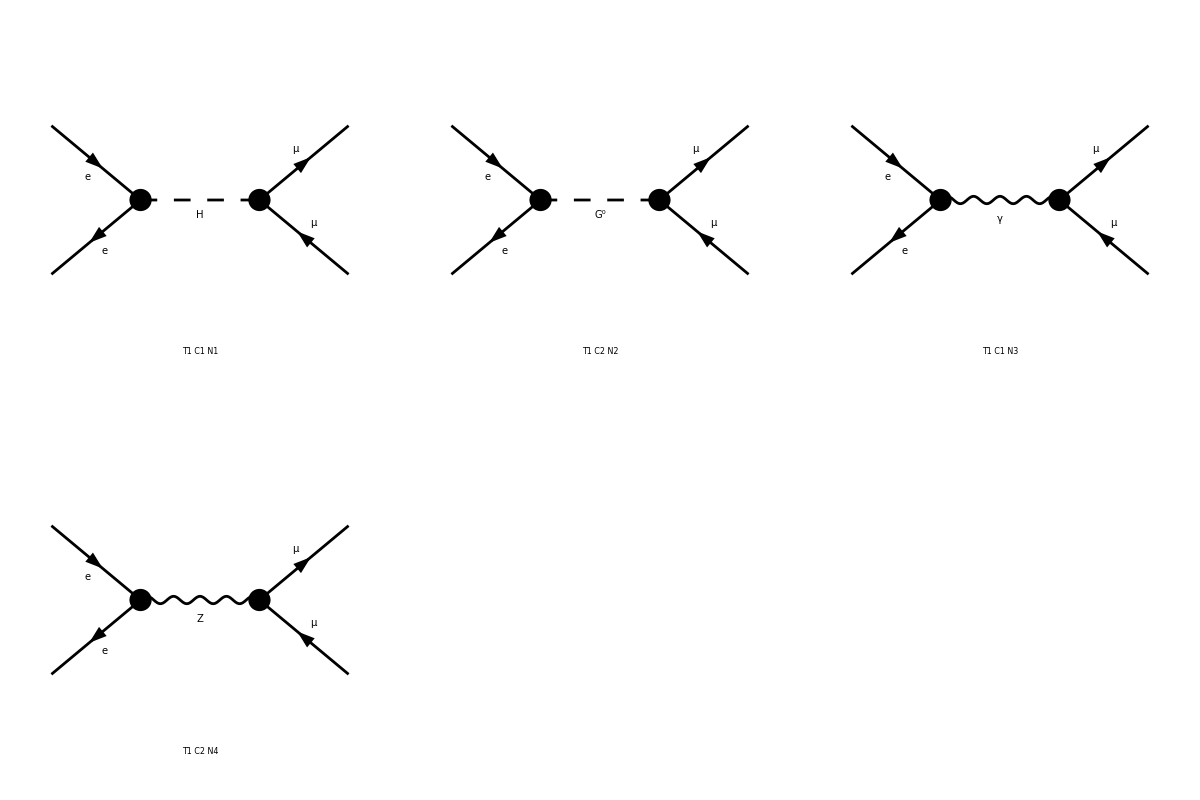

FeynArtsGraphics[{e,e}→{\mu,\mu}][([T1 C1 N1] | [T1 C2 N2] | [T1 C1 N3]
[T1 C2 N4] | Null | Null
Null | Null | Null)]

```mathematica
Paint[diagrams]
```

### Insert Particles (again...)

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 1 Classes insertion

> Top. 1: 1 diagram

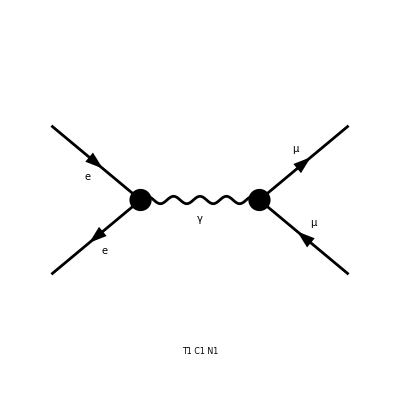

```mathematica
diagrams=InsertFields[topologies,{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]},InsertionLevel->{Classes},
	ExcludeParticles->{V[2],S[1],S[2]}];
Paint[diagrams];
```

### Pass the diagram to FormCalc

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->VA];
matrix=SquaredME[amplitude]//.HelicityME[amplitude]//.Hel[_]->0
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM... running FORM...

ok

> 1 helicity matrix elements

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

ok

8 Alfa2 π^2 (2 ME2^2+4 ME2 MM2+2 MM2^2+S^2-4 ME2 T-4 MM2 T+2 S T+2 T^2) Den[S,0]^2

-Graphics-

```mathematica
matrix//.{Den[p2_,m2_]:>1/(p2-m2),Alfa->e^2/(4π),Alfa2->(e^2/(4π))^2,ME2->0}
```

(e^4 (2 MM2^2+S^2-4 MM2 T+2 S T+2 T^2))/(2 S^2)

```mathematica
%//.{S->4 EE^2,T->MM^2-2(EE^2-EE √(EE^2-MM^2)CosTheta)}
```

(e^4 (16 EE^4+2 MM2^2+8 EE^2 (-2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)-4 MM2 (-2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)+2 (-2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2))/(32 EE^4)

```mathematica
Collect[FullSimplify[%],{e,CosTheta}]
```

e^4 ((CosTheta^2 (EE^2-MM2))/(4 EE^2)+(EE^2+MM2)/(4 EE^2))

Many Traps!!!!!!!!!!!!!!!!

### Doing again with pacience.

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->Weyl](*Default*)
amplitude//.Abbr[]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM...

ok

Amp[{ME,ME}→{MM,MM}][-8 AbbSum150 Alfa π Den[S,0]]

Amp[{ME,ME}→{MM,MM}][-8 Alfa π Den[S,0] (((v̇ 2|7|v4)) ((u̇ 3|6|u1))+((v̇ 2|6|v4)) ((u̇ 3|7|u1))+((v̇ 2|6,-1|u̇ 3)) ((u1|6,-1|v4))+((v̇ 2|7,-1|u̇ 3)) ((u1|7,-1|v4)))]

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->Chiral]
amplitude//.Abbr[]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM...

ok

Amp[{ME,ME}→{MM,MM}][-4 Alfa π Den[S,0] Mat[F14]-4 Alfa π Den[S,0] Mat[F15]-4 Alfa π Den[S,0] Mat[F16]-4 Alfa π Den[S,0] Mat[F17]]

Amp[{ME,ME}→{MM,MM}][-4 Alfa π Den[S,0] Mat[(<v1|6,Lor[1]|u2>) (<u3|6,Lor[1]|v4>)]-4 Alfa π Den[S,0] Mat[(<v1|7,Lor[1]|u2>) (<u3|6,Lor[1]|v4>)]-4 Alfa π Den[S,0] Mat[(<v1|6,Lor[1]|u2>) (<u3|7,Lor[1]|v4>)]-4 Alfa π Den[S,0] Mat[(<v1|7,Lor[1]|u2>) (<u3|7,Lor[1]|v4>)]]

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->VA]
amplitude//.Abbr[]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM...

ok

Amp[{ME,ME}→{MM,MM}][-4 Alfa π Den[S,0] Mat[F18]]

Amp[{ME,ME}→{MM,MM}][-4 Alfa π Den[S,0] Mat[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)]]

```mathematica
SquaredME[amplitude]
```

16 Alfa2 π^2 Den[S,0]^2 Mat[F18,F18]

```mathematica
SquaredHelicityME=SquaredME[amplitude]//.HelicityME[amplitude]//.Abbr[]
```

> 1 helicity matrix elements

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM...

ok

8 Alfa2 π^2 (2 ME2^2+4 ME2 MM2+2 MM2^2+S^2-4 ME2 T-4 MM2 T+2 S T+2 T^2) Den[S,0]^2

```mathematica
SquaredHelicityME//.{Hel[1]->0,Hel[2]->0,Hel[3]->0,Hel[4]->0}
```

8 Alfa2 π^2 (2 ME2^2+4 ME2 MM2+2 MM2^2+S^2-4 ME2 T-4 MM2 T+2 S T+2 T^2) Den[S,0]^2

This is AVERAGE! So we have to multiply by four.

```mathematica
MatrixElement=2^2*(SquaredHelicityME//.{Hel[_]->0})
```

32 Alfa2 π^2 (2 ME2^2+4 ME2 MM2+2 MM2^2+S^2-4 ME2 T-4 MM2 T+2 S T+2 T^2) Den[S,0]^2

```mathematica
MatrixElement//.{Den[p2_,m2_]:>1/(p2-m2),Alfa->e^2/(4π),Alfa2->(e^2/(4π))^2,ME2->0}//.{S->4 EE^2,T->MM^2-2(EE^2-EE √(EE^2-MM^2)CosTheta)}
```

(e^4 (16 EE^4+2 MM2^2+8 EE^2 (-2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)-4 MM2 (-2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)+2 (-2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2))/(8 EE^4)

```mathematica
Collect[FullSimplify[%],{e,CosTheta}]
```

e^4 ((CosTheta^2 (EE^2-MM2))/EE^2+(EE^2+MM2)/EE^2)

-Graphics-